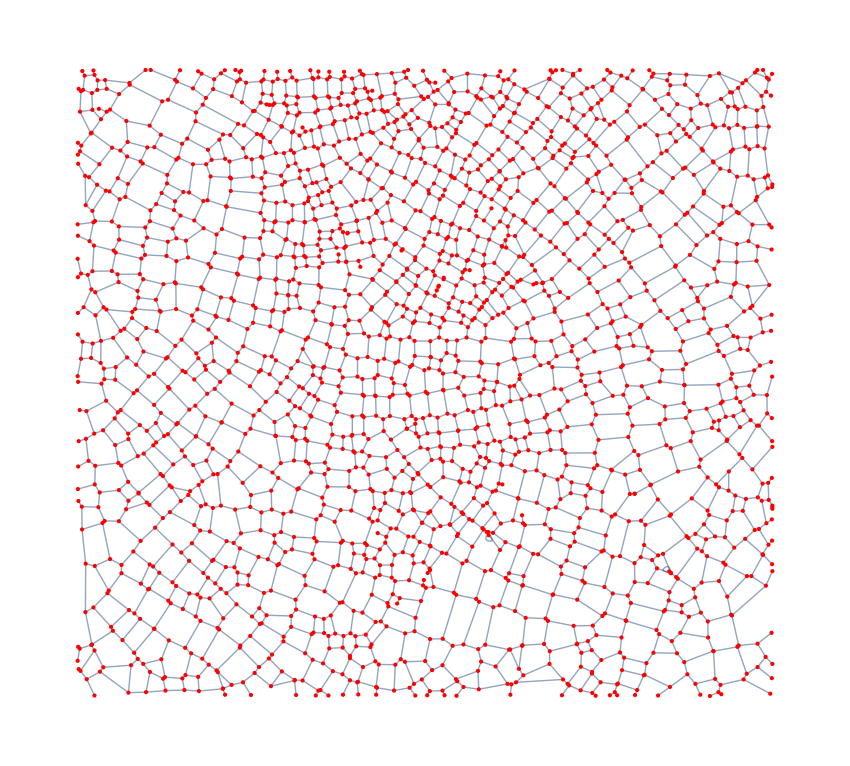

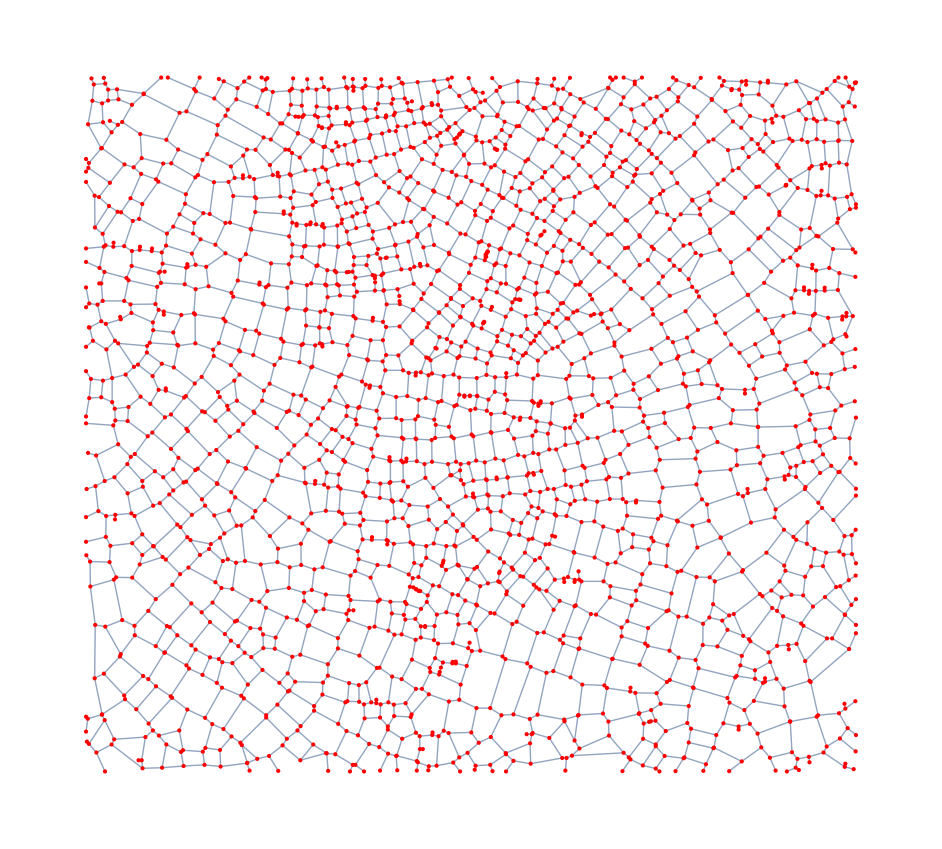

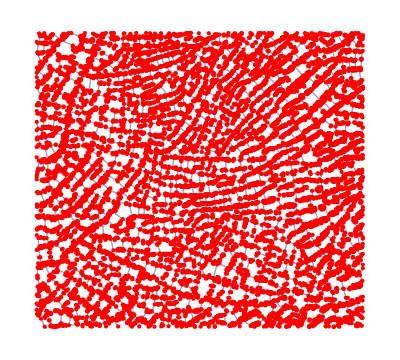

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[i11,ig1,ig2,ig3]
i11=ColorNegate@Binarize@Sharpen@-Graphics-;
(* {MorphologicalGraph[ Thinning[Dilation[i11,3],30],VertexStyle->Red] ,MorphologicalGraph[ Thinning[ ColorNegate@Opening[ColorNegate@i11,3.8],30],VertexStyle->Red]  ,MorphologicalGraph[Thinning[i11,30],VertexStyle->Red] }  *)
 ig1=MorphologicalGraph[ Thinning[Dilation[i11,3],30],VertexStyle->Red]
ig2=MorphologicalGraph[ Thinning[ ColorNegate@Opening[ColorNegate@i11,3.8],30],VertexStyle->Red]
ig3=MorphologicalGraph[Thinning[i11,30],VertexStyle->Red]
{Show[i11,ig1],Show[i11,ig2],Show[i11,ig3]}

(* { Thinning[Dilation[i11,3],30] , Thinning[ ColorNegate@Opening[ColorNegate@i11,3.8],30]  , Thinning[i11,30] }
{Manipulate[Thinning[Dilation[i11,c1],c],{c,0,30 ,1},{c1,1,10}],Manipulate[Thinning[ ColorNegate@Opening[ColorNegate@i11,c1] ,c],{c,0,30 ,1},{c1,1,10}]} *)
```